### Global initialization

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*Needs["Notation`"]*)
```

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

### Formulas needed for calculations

```mathematica
tfM[rotationVariable_,rotationVector_,translationVector_]:=Simplify[ArrayFlatten[{{RotationMatrix[rotationVariable,rotationVector],0},{skew[translationVector].RotationMatrix[rotationVariable,rotationVector],RotationMatrix[rotationVariable,rotationVector]}}]]
```

```mathematica
itfM[rotationVariable_,rotationVector_,translationVector_]:=Simplify[ArrayFlatten[{{Transpose[RotationMatrix[rotationVariable,rotationVector]],0},{-Transpose[RotationMatrix[rotationVariable,rotationVector]].skew[translationVector],Transpose[RotationMatrix[rotationVariable,rotationVector]]}}]]
```

```mathematica
tfF[rotationVariable_,rotationVector_,translationVector_]:=Simplify[ArrayFlatten[{{RotationMatrix[rotationVariable,rotationVector],skew[translationVector].RotationMatrix[rotationVariable,rotationVector]},{0,RotationMatrix[rotationVariable,rotationVector]}}]]
```

```mathematica
itfF[rotationVariable_,rotationVector_,translationVecAW664AAtor_]:=Simplify[ArrayFlatten[{{Transpose[RotationMatrix[rotationVariable,rotationVector]],-Transpose[RotationMatrix[rotationVariable,rotationVector]].skew[translationVector]},{0,Transpose[RotationMatrix[rotationVariable,rotationVector]]}}]]
```

```mathematica
(*tfM4[rotVar_,rotVec_,transVec_]:=ArrayFlatten[{{RotationMatrix[rotVar,rotVec],Transpose[{transVec}]},{0,1}}]*)
```

```mathematica
(*itfM4[rotVar_,rotVec_,transVec_]:=ArrayFlatten[{{Transpose[RotationMatrix[rotVar,rotVec]],-Transpose[{transVec}]},{0,1}}]*)
```

```mathematica
skew[x_]/;(Equal[Length[x],3]):={{0,-x[[3]],x[[2]]},{x[[3]],0,-x[[1]]},{-x[[2]],x[[1]],0}}
```

```mathematica
skewM6[x_]/;(Equal[Length[x],6]):=Simplify[ArrayFlatten[{{skew[x[[1;;3]]],0},{skew[x[[4;;6]]],skew[x[[1;;3]]]}}]]
```

```mathematica
skewF6[x_]/;(Equal[Length[x],6]):=Simplify[ArrayFlatten[{{skew[x[[1;;3]]],skew[x[[4;;6]]]},{0,skew[x[[1;;3]]]}}]]
```

```mathematica
vectorize[x_/;(Equal[Dimensions[x],{3,3}])]:=Simplify[{(x[[3,2]]-x[[2,3]]),(x[[1,3]]-x[[3,1]]),(x[[2,1]]-x[[1,2]])}/2]
```

```mathematica
tfM[frameDefinition_,startFrame_,endFrame_]/;MatchQ[frameDefinition,_Association]:=Module[{graph=Graph[Map[frameDefinition[#]["connection"]&,Keys[frameDefinition]]]},
If[Equal[startFrame,endFrame],DiagonalMatrix[{1,1,1,1,1,1}],If[Apply[Less,Map[FirstPosition[VertexList[graph],#][[1]]&,{startFrame,endFrame}]],
Simplify[Dot@@Map[tfM[frameDefinition[#]["rotVar"],frameDefinition[#]["rotVec"],frameDefinition[#]["transVec"]]&,Flatten[Map[Position[Map[frameDefinition[#][["connection"]]&,Keys[frameDefinition]],#]&,EdgeList[Subgraph[graph,FindShortestPath[graph,startFrame,endFrame]]]]]]],Simplify[Dot@@Reverse[Map[itfM[T1[#]["rotVar"],T1[#]["rotVec"],T1[#]["transVec"]]&,Flatten[Map[Position[Map[frameDefinition[#][["connection"]]&,Keys[frameDefinition]],#]&,EdgeList[Subgraph[graph,FindShortestPath[graph,endFrame,startFrame]]]]]]]]]]]
```

```mathematica
tfF[frameDefinition_,startFrame_,endFrame_]/;MatchQ[frameDefinition,_Association]:=Module[{graph=Graph[Map[frameDefinition[#]["connection"]&,Keys[frameDefinition]]]},
If[Equal[startFrame,endFrame],DiagonalMatrix[{1,1,1,1,1,1}],If[Apply[Less,Map[FirstPosition[VertexList[graph],#][[1]]&,{startFrame,endFrame}]],
Simplify[Dot@@Map[tfF[frameDefinition[#]["rotVar"],frameDefinition[#]["rotVec"],frameDefinition[#]["transVec"]]&,Flatten[Map[Position[Map[frameDefinition[#][["connection"]]&,Keys[frameDefinition]],#]&,EdgeList[Subgraph[graph,FindShortestPath[graph,startFrame,endFrame]]]]]]],Simplify[Dot@@Reverse[Map[itfF[T1[#]["rotVar"],T1[#]["rotVec"],T1[#]["transVec"]]&,Flatten[Map[Position[Map[frameDefinition[#][["connection"]]&,Keys[frameDefinition]],#]&,EdgeList[Subgraph[graph,FindShortestPath[graph,endFrame,startFrame]]]]]]]]]]]
```

```mathematica
(*tfM4[frameDefinition_,startFrame_,endFrame_]/;MatchQ[frameDefinition,_Association]:=Module[{graph=Graph[Map[frameDefinition[#]["connection"]&,Keys[frameDefinition]]]},
If[Equal[startFrame,endFrame],DiagonalMatrix[{1,1,1,1}],If[Apply[Less,Map[FirstPosition[VertexList[graph],#][[1]]&,{startFrame,endFrame}]],
Simplify[Dot@@Map[tfM4[frameDefinition[#]["rotVar"],frameDefinition[#]["rotVec"],frameDefinition[#]["transVec"]]&,Flatten[Map[Position[Map[frameDefinition[#][["connection"]]&,Keys[frameDefinition]],#]&,EdgeList[Subgraph[graph,FindShortestPath[graph,startFrame,endFrame]]]]]]],Simplify[Dot@@Reverse[Map[itfM4[T1[#]["rotVar"],T1[#]["rotVec"],T1[#]["transVec"]]&,Flatten[Map[Position[Map[frameDefinition[#][["connection"]]&,Keys[frameDefinition]],#]&,EdgeList[Subgraph[graph,FindShortestPath[graph,endFrame,startFrame]]]]]]]]]]]*)
```

```mathematica
tW[frameDefinition_,wrtFrame_,motionOfFrame_,expressedInFrame_]:=Module[{matrix=Simplify[tfM[frameDefinition,expressedInFrame,wrtFrame].D[tfM[frameDefinition,wrtFrame,motionOfFrame],t].tfM[frameDefinition,motionOfFrame,expressedInFrame]]},Flatten[{vectorize[matrix[[1;;3,1;;3]]],vectorize[matrix[[4;;6,1;;3]]]}]]
```

```mathematica
(*tW4[frameDefinition_,wrtFrame_,motionOfFrame_,expressedInFrame_]:=Simplify[tfM4[frameDefinition,expressedInFrame,wrtFrame].D[tfM4[frameDefinition,wrtFrame,motionOfFrame],t].tfM4[frameDefinition,motionOfFrame,expressedInFrame]]*)
```

```mathematica
tW[x_]/;Equal[Length[x],4]:=Flatten[{vectorize[x[[1;;3,1;;3]]],x[[1;;3,4]]}]
```

```mathematica
adj[frameDefinition_,wrtFrame_,motionOfFrame_,expressedInFrame_]:=Simplify[tfM[frameDefinition,expressedInFrame,wrtFrame].D[tfM[frameDefinition,wrtFrame,motionOfFrame],t].tfM[frameDefinition,motionOfFrame,expressedInFrame]]
```

```mathematica
vectorize6[x_]/;Equal[Length[x],6]:=Flatten[{vectorize[x[[1;;3,1;;3]]],vectorize[x[[4;;6,1;;3]]]}]
```

### Model definition

```mathematica
T1=<|1-> <|{"connection"->DirectedEdge["frame0","frameA"],"rotVar"-> Subscript[θ, 1][t],"rotVec"->{1,0,0},"transVec"->{0,0,0}}|>,
2-> <|{"connection"->DirectedEdge["frameA","frameB"],"rotVar"-> 0,"rotVec"->{1,0,0},"transVec"->{0,0,-l}}|>,3-> <|{"connection"->DirectedEdge["frameB","frameC"],"rotVar"-> Subscript[θ, 2][t],"rotVec"->{1,0,0},"transVec"->{0,0,0}}|>,
4-> <|{"connection"->DirectedEdge["frameC","frameD"],"rotVar"-> 0,"rotVec"->{1,0,0},"transVec"->{0,0,-l}}|>,
5-> <|{"connection"->DirectedEdge["frameD","frameE"],"rotVar"-> Subscript[θ, 3][t],"rotVec"->{1,0,0},"transVec"->{0,0,0}}|>,
6-> <|{"connection"->DirectedEdge["frameE","frameF"],"rotVar"-> 0,"rotVec"->{1,0,0},"transVec"->{0,0,-l}}|>
|>;
```

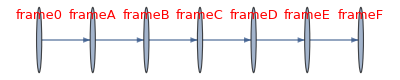

```mathematica
T2=Graph[Map[T1[#]["connection"]&,Keys[T1]],VertexLabels->Placed["Name",Top],VertexLabelStyle->Directive[Red,13]]
```

```mathematica
params={m-> 9.375,w-> 0.05, l-> 0.5};
```

### Analytics calculations

#### Inertia

```mathematica
I1=ArrayFlatten[{{DiagonalMatrix[{1/12 m (w^2+l^2),1/12 m (w^2+l^2),1/12 m (w^2+w^2)}],0},{0,DiagonalMatrix[{m,m,m}]}}]
```

{{1/12 m (l^2+w^2),0,0,0,0,0},{0,1/12 m (l^2+w^2),0,0,0,0},{0,0,(m w^2)/6,0,0,0},{0,0,0,m,0,0},{0,0,0,0,m,0},{0,0,0,0,0,m}}

```mathematica
I01=(tfF[0,{1,0,0},{0,0,-l/2}].I1.itfM[0,{1,0,0},{0,0,-l/2}])/.params;
```

```mathematica
I03=I02=I01;
```

```mathematica
I03//MatrixForm
```

(0.783203 | 0 | 0 | 0 | 2.34375 | 0
0 | 0.783203 | 0 | -2.34375 | 0 | 0
0 | 0 | 0.00390625 | 0 | 0 | 0
0 | -2.34375 | 0 | 9.375 | 0 | 0
2.34375 | 0 | 0 | 0 | 9.375 | 0
0 | 0 | 0 | 0 | 0 | 9.375)

#### Motion quantities e.g. velocity/accelaration

```mathematica
v1=tW[T1,"frame0","frameA","frameA"]
```

{θ_1'[t],0,0,0,0,0}

```mathematica
v2=tW[T1,"frameA","frameC","frameC"]+tW[T1,"frame0","frameA","frameC"];
```

```mathematica
v3=tW[T1,"frameC","frameE","frameE"]+tW[T1,"frameA","frameC","frameE"]+tW[T1,"frame0","frameA","frameE"];
```

```mathematica
a1=D[tW[T1,"frame0","frameA","frameA"],t];
```

```mathematica
a2=D[tW[T1,"frameA","frameC","frameC"],t]+tfM[T1,"frameC","frameA"].D[tW[T1,"frame0","frameA","frameA"],t]+skewM6[tW[T1,"frame0","frameA","frameC"]].tW[T1,"frameA","frameC","frameC"];
```

```mathematica
a3=D[tW[T1,"frameC","frameE","frameE"],t]+tfM[T1,"frameE","frameC"].(D[tW[T1,"frameA","frameC","frameC"],t]+D[tW[T1,"frame0","frameA","frameC"],t])+skewM6[tW[T1,"frameA","frameC","frameE"]+tW[T1,"frame0","frameA","frameE"]].tW[T1,"frameC","frameE","frameE"];
```

```mathematica
v3//MatrixForm
```

(θ_1'[t]+θ_2'[t]+θ_3'[t]
0
0
0
2 l Cos[θ_2[t]/2] Cos[θ_2[t]/2+θ_3[t]] θ_1'[t]+l Cos[θ_3[t]] θ_2'[t]
-2 l Cos[θ_2[t]/2] Sin[θ_2[t]/2+θ_3[t]] θ_1'[t]-l Sin[θ_3[t]] θ_2'[t])

```mathematica
a3//MatrixForm
```

(θ_1''[t]+θ_2''[t]+θ_3''[t]
0
0
0
-l ((Sin[θ_3[t]]+Sin[θ_2[t]+θ_3[t]]) θ_1'[t]+Sin[θ_3[t]] θ_2'[t]) θ_3'[t]+Cos[θ_3[t]] (-l Sin[θ_2[t]] θ_1'[t] θ_2'[t]+l Cos[θ_2[t]] θ_1''[t])+Sin[θ_3[t]] (-l Cos[θ_2[t]] θ_1'[t] θ_2'[t]-l Sin[θ_2[t]] θ_1''[t])+l Cos[θ_3[t]] (θ_1''[t]+θ_2''[t])
-l ((Cos[θ_3[t]]+Cos[θ_2[t]+θ_3[t]]) θ_1'[t]+Cos[θ_3[t]] θ_2'[t]) θ_3'[t]-Sin[θ_3[t]] (-l Sin[θ_2[t]] θ_1'[t] θ_2'[t]+l Cos[θ_2[t]] θ_1''[t])+Cos[θ_3[t]] (-l Cos[θ_2[t]] θ_1'[t] θ_2'[t]-l Sin[θ_2[t]] θ_1''[t])-l Sin[θ_3[t]] (θ_1''[t]+θ_2''[t]))

#### Force quantities

```mathematica
w3=I03.(a3-tfM[T1,"frameE","frame0"].{0,0,0,0,0,-g})+skewF6[v3].(I03.v3)//Simplify;
```

```mathematica
w2=I02.(a2-tfM[T1,"frameC","frame0"].{0,0,0,0,0,-g})+skewF6[v2].(I02.v2)+tfF[T1,"frameC","frameE"].w3//Simplify;
```

```mathematica
w1=I01.(a1-tfM[T1,"frameA","frame0"].{0,0,0,0,0,-g})+skewF6[v1].(I01.v1)+tfF[T1,"frameA","frameC"].w2//Simplify;
```

```mathematica
w3//Simplify//MatrixForm
```

(2.34375 g Sin[θ_1[t]+θ_2[t]+θ_3[t]]+(2.34375 l Sin[θ_3[t]]+2.34375 l Sin[θ_2[t]+θ_3[t]]) θ_1'[t]^2+4.6875 l Sin[θ_3[t]] θ_1'[t] θ_2'[t]+2.34375 l Sin[θ_3[t]] θ_2'[t]^2+0.783203 θ_1''[t]+2.34375 l Cos[θ_3[t]] θ_1''[t]+2.34375 l Cos[θ_2[t]+θ_3[t]] θ_1''[t]+0.783203 θ_2''[t]+2.34375 l Cos[θ_3[t]] θ_2''[t]+0.783203 θ_3''[t]
0.
0.
0.
9.375 g Sin[θ_1[t]+θ_2[t]+θ_3[t]]+(9.375 l Sin[θ_3[t]]+9.375 l Sin[θ_2[t]+θ_3[t]]) θ_1'[t]^2+18.75 l Sin[θ_3[t]] θ_1'[t] θ_2'[t]+9.375 l Sin[θ_3[t]] θ_2'[t]^2+2.34375 θ_1''[t]+9.375 l Cos[θ_3[t]] θ_1''[t]+9.375 l Cos[θ_2[t]+θ_3[t]] θ_1''[t]+2.34375 θ_2''[t]+9.375 l Cos[θ_3[t]] θ_2''[t]+2.34375 θ_3''[t]
9.375 g Cos[θ_1[t]+θ_2[t]+θ_3[t]]+(2.34375+9.375 l Cos[θ_3[t]]+9.375 l Cos[θ_2[t]+θ_3[t]]) θ_1'[t]^2+(2.34375+9.375 l Cos[θ_3[t]]) θ_2'[t]^2+4.6875 θ_2'[t] θ_3'[t]+2.34375 θ_3'[t]^2+θ_1'[t] ((4.6875+18.75 l Cos[θ_3[t]]) θ_2'[t]+4.6875 θ_3'[t])-9.375 l Sin[θ_3[t]] θ_1''[t]-9.375 l Sin[θ_2[t]+θ_3[t]] θ_1''[t]-9.375 l Sin[θ_3[t]] θ_2''[t])

```mathematica
w2//Simplify//MatrixForm
```

(2.34375 g Sin[θ_1[t]+θ_2[t]]+9.375 g l Sin[θ_1[t]+θ_2[t]]+2.34375 g Sin[θ_1[t]+θ_2[t]+θ_3[t]]+l ((2.34375+9.375 l) Sin[θ_2[t]]+2.34375 Sin[θ_2[t]+θ_3[t]]) θ_1'[t]^2-4.6875 l Sin[θ_3[t]] θ_1'[t] θ_3'[t]-4.6875 l Sin[θ_3[t]] θ_2'[t] θ_3'[t]-2.34375 l Sin[θ_3[t]] θ_3'[t]^2+1.56641 θ_1''[t]+9.375 l^2 θ_1''[t]+2.34375 l Cos[θ_2[t]] θ_1''[t]+9.375 l^2 Cos[θ_2[t]] θ_1''[t]+4.6875 l Cos[θ_3[t]] θ_1''[t]+2.34375 l Cos[θ_2[t]+θ_3[t]] θ_1''[t]+1.56641 θ_2''[t]+9.375 l^2 θ_2''[t]+4.6875 l Cos[θ_3[t]] θ_2''[t]+0.783203 θ_3''[t]+2.34375 l Cos[θ_3[t]] θ_3''[t]
0.
0.
0.
18.75 g Cos[θ_2[t]] Sin[θ_1[t]]+18.75 g Cos[θ_1[t]] Sin[θ_2[t]]+(18.75 l Sin[θ_2[t]]-2.34375 Sin[θ_3[t]]) θ_1'[t]^2-2.34375 Sin[θ_3[t]] θ_2'[t]^2+Sin[θ_3[t]] θ_1'[t] (-4.6875 θ_2'[t]-4.6875 θ_3'[t])-4.6875 Sin[θ_3[t]] θ_2'[t] θ_3'[t]-2.34375 Sin[θ_3[t]] θ_3'[t]^2+2.34375 θ_1''[t]+9.375 l θ_1''[t]+18.75 l Cos[θ_2[t]] θ_1''[t]+2.34375 Cos[θ_3[t]] θ_1''[t]+2.34375 θ_2''[t]+9.375 l θ_2''[t]+2.34375 Cos[θ_3[t]] θ_2''[t]+2.34375 Cos[θ_3[t]] θ_3''[t]
18.75 g Cos[θ_1[t]] Cos[θ_2[t]]-18.75 g Sin[θ_1[t]] Sin[θ_2[t]]+(2.34375+9.375 l+18.75 l Cos[θ_2[t]]+2.34375 Cos[θ_3[t]]) θ_1'[t]^2+(2.34375+9.375 l+2.34375 Cos[θ_3[t]]) θ_2'[t]^2+4.6875 Cos[θ_3[t]] θ_2'[t] θ_3'[t]+2.34375 Cos[θ_3[t]] θ_3'[t]^2+θ_1'[t] ((4.6875+18.75 l+4.6875 Cos[θ_3[t]]) θ_2'[t]+4.6875 Cos[θ_3[t]] θ_3'[t])-18.75 l Sin[θ_2[t]] θ_1''[t]+2.34375 Sin[θ_3[t]] θ_1''[t]+2.34375 Sin[θ_3[t]] θ_2''[t]+2.34375 Sin[θ_3[t]] θ_3''[t])

```mathematica
w1//Simplify//MatrixForm
```

(2.34375 g Sin[θ_1[t]]+18.75 g l Sin[θ_1[t]]+2.34375 g Sin[θ_1[t]+θ_2[t]]+9.375 g l Sin[θ_1[t]+θ_2[t]]+2.34375 g Sin[θ_1[t]+θ_2[t]+θ_3[t]]+l ((-2.34375-9.375 l) Sin[θ_2[t]]-2.34375 Sin[θ_2[t]+θ_3[t]]) θ_2'[t]^2+l (-4.6875 Sin[θ_3[t]]-4.6875 Sin[θ_2[t]+θ_3[t]]) θ_2'[t] θ_3'[t]-2.34375 l Sin[θ_3[t]] θ_3'[t]^2-2.34375 l Sin[θ_2[t]+θ_3[t]] θ_3'[t]^2+l θ_1'[t] (((-4.6875-18.75 l) Sin[θ_2[t]]-4.6875 Sin[θ_2[t]+θ_3[t]]) θ_2'[t]+(-4.6875 Sin[θ_3[t]]-4.6875 Sin[θ_2[t]+θ_3[t]]) θ_3'[t])+2.34961 θ_1''[t]+28.125 l^2 θ_1''[t]+4.6875 l Cos[θ_2[t]] θ_1''[t]+18.75 l^2 Cos[θ_2[t]] θ_1''[t]+4.6875 l Cos[θ_3[t]] θ_1''[t]+4.6875 l Cos[θ_2[t]+θ_3[t]] θ_1''[t]+1.56641 θ_2''[t]+9.375 l^2 θ_2''[t]+2.34375 l Cos[θ_2[t]] θ_2''[t]+9.375 l^2 Cos[θ_2[t]] θ_2''[t]+4.6875 l Cos[θ_3[t]] θ_2''[t]+2.34375 l Cos[θ_2[t]+θ_3[t]] θ_2''[t]+0.783203 θ_3''[t]+2.34375 l Cos[θ_3[t]] θ_3''[t]+2.34375 l Cos[θ_2[t]+θ_3[t]] θ_3''[t]
0.
0.
0.
28.125 g Sin[θ_1[t]]+((-2.34375-9.375 l) Sin[θ_2[t]]-2.34375 Sin[θ_2[t]+θ_3[t]]) θ_1'[t]^2+((-2.34375-9.375 l) Sin[θ_2[t]]-2.34375 Sin[θ_2[t]+θ_3[t]]) θ_2'[t]^2-4.6875 Sin[θ_2[t]+θ_3[t]] θ_2'[t] θ_3'[t]-2.34375 Sin[θ_2[t]+θ_3[t]] θ_3'[t]^2+θ_1'[t] (((-4.6875-18.75 l) Sin[θ_2[t]]-4.6875 Sin[θ_2[t]+θ_3[t]]) θ_2'[t]-4.6875 Sin[θ_2[t]+θ_3[t]] θ_3'[t])+2.34375 θ_1''[t]+18.75 l θ_1''[t]+2.34375 Cos[θ_2[t]] θ_1''[t]+9.375 l Cos[θ_2[t]] θ_1''[t]+2.34375 Cos[θ_2[t]+θ_3[t]] θ_1''[t]+2.34375 Cos[θ_2[t]] θ_2''[t]+9.375 l Cos[θ_2[t]] θ_2''[t]+2.34375 Cos[θ_2[t]+θ_3[t]] θ_2''[t]+2.34375 Cos[θ_2[t]+θ_3[t]] θ_3''[t]
28.125 g Cos[θ_1[t]]+(2.34375+18.75 l+(2.34375+9.375 l) Cos[θ_2[t]]+2.34375 Cos[θ_2[t]+θ_3[t]]) θ_1'[t]^2+((2.34375+9.375 l) Cos[θ_2[t]]+2.34375 Cos[θ_2[t]+θ_3[t]]) θ_2'[t]^2+4.6875 Cos[θ_2[t]+θ_3[t]] θ_2'[t] θ_3'[t]+2.34375 Cos[θ_2[t]+θ_3[t]] θ_3'[t]^2+θ_1'[t] (((4.6875+18.75 l) Cos[θ_2[t]]+4.6875 Cos[θ_2[t]+θ_3[t]]) θ_2'[t]+4.6875 Cos[θ_2[t]+θ_3[t]] θ_3'[t])+2.34375 Sin[θ_2[t]] θ_1''[t]+9.375 l Sin[θ_2[t]] θ_1''[t]+2.34375 Sin[θ_2[t]+θ_3[t]] θ_1''[t]+2.34375 Sin[θ_2[t]] θ_2''[t]+9.375 l Sin[θ_2[t]] θ_2''[t]+2.34375 Sin[θ_2[t]+θ_3[t]] θ_2''[t]+2.34375 Sin[θ_2[t]+θ_3[t]] θ_3''[t])